```mathematica
Get["new1through5Sequential.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Get["OG_Josh_o1through4.m"]
```

```mathematica
For[k = 0, k ≤4,k++,
Josh[k] = Exp[γ  (y  - x)]* Sum[(-1/2)^j (γ)^(2j) * o[j], {j, 0, k}]
]
```

```mathematica
Clear[o]
```

```mathematica
GaussianApprox= (2 π x (1-x) t)^(-1/2) Exp[-(y-(x+2Ne α Λ x (1-x) t / W))^2 / (2 x (1-x) t)]
```

(ⅇ^(-(-x+y-(2 Ne t (1-x) x α Λ)/W)^2/(2 t (1-x) x)))/(√(2 π) √(t (1-x) x))

```mathematica
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
neutral = Kimura[x,y,t,10];
```

```mathematica
kimplot = Kimura[x,y,t,n];
```

```mathematica
kthkimura[x_,y_,t_,m_] := 4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t];
```

```mathematica
kythplot = kthkimura[x,y,t,n];
```

(4 ⅇ^(-1/2 n (1+n) t) (1+2 n) (1-x) x GegenbauerC[-1+n,3/2,1-2 x] GegenbauerC[-1+n,3/2,1-2 y])/(n (1+n))

```mathematica
Plot[Evaluate[Table[kythplot /. {x-> 0.25, t-> 0.1}, {n,1,5}]],{y,0,1},PlotLegends->{Table[n,{n,1,5}]},
PlotLabels->Table[TextString[n],{n,1,5}]]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\firstkkimura.svg",%15,"SVG"]
```

C:\Users\natha\Documents\firstkkimura.svg

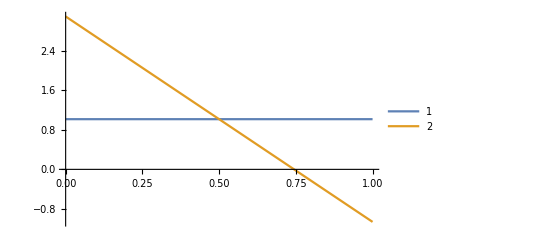

```mathematica
Plot[{Kimura[x,y,t,1] /. {x-> 0.25, t-> 0.1},Kimura[x,y,t,2] /. {x-> 0.25, t-> 0.1}},{y,0,1},PlotLegends->{"1","2"}]
```

```mathematica
Plot[Evaluate[Table[kimplot /. {x-> 0.25, t-> 0.1}, {n,1,5}]],{y,0,1},PlotLegends->{Table[n,{n,1,5}]},
PlotLabels->Table[TextString[n],{n,1,5}]]
```

-Graphics-

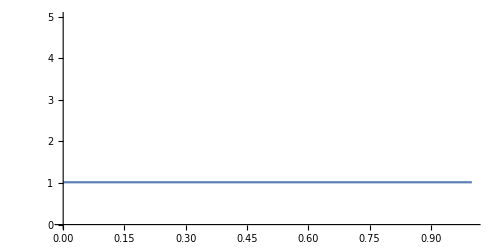
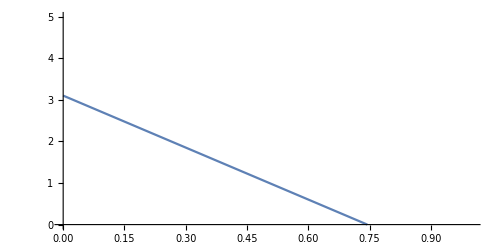
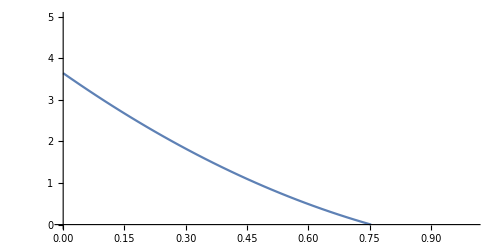
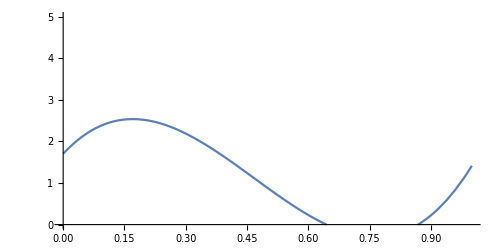
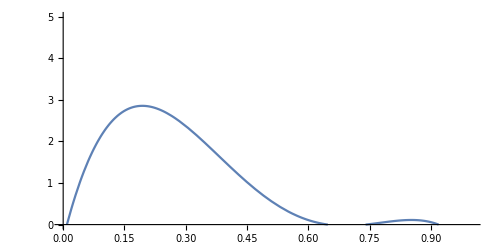
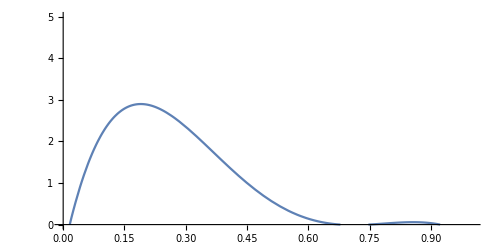
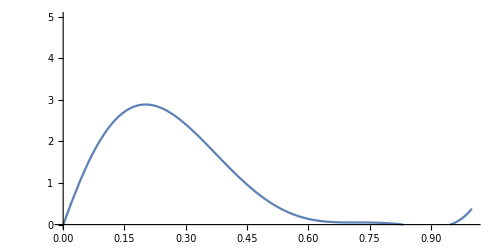
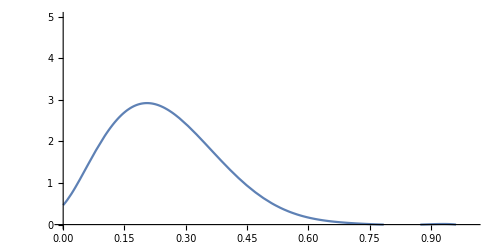

```mathematica
Clear[Anim];
Anim=Table[Plot[Evaluate[kimplot/. {x->0.25,t-> 0.1,n->bigN}],
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLegends->TextString@Row@{"n=",bigN}, 
PlotRange->{{0,1},{0,5}}],{bigN,1,15}]
```

```mathematica
Export["neutralConvergence.gif",Anim,"DisplayDurations"->0.75]
```

neutralConvergence.gif

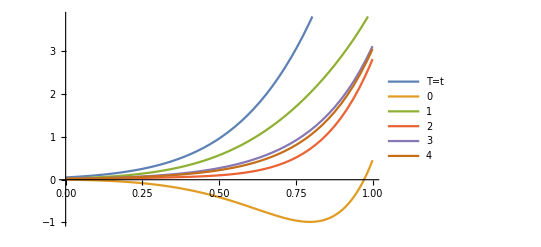

```mathematica
Plot[Evaluate[Table[SimplifiedHayward[k]/. {x->0.5, t->0.5,Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{k,0, 5}]],{y,0,1},PlotLegends->{Table[k,{k,0,5}]}]
```

```mathematica
Table[TextString[k],{k,0,5}]
```

{0,1,2,3,4,5}

```mathematica
First[{"0","1","2","3","4","5"}]
```

0

```mathematica
Clear[Anim]
```

```mathematica
NumberForm
```

```mathematica
Anim=Table[Plot[Evaluate[Table[SimplifiedHayward[k]/. {x->0.5,t-> 0.1,Ne->500, Λ -> 1, W->1, VG->.00001111},{k,0, 5}]],
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLegends->TextString@Row@{"α=",NumberForm[α, {6,5}]}, 
PlotLabels->Table[TextString[k],{k,0,5}],
PlotRange->{{0,1},{0,10}}],{α,.0001,.01,.00025}];
```

```mathematica
Export["selectionConvergence.gif",Anim,"DisplayDurations"->0.3]
```

selectionConvergence.gif

```mathematica
Length[Anim]
```

40

```mathematica
Anim[[40]]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\BigAlphaConvergence.svg",%59,"SVG"]
```

C:\Users\natha\Documents\BigAlphaConvergence.svg

```mathematica
Anim=Table[Plot[Evaluate[Table[SimplifiedHayward[k]/. {x->0.5,Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{k,0, 5}]],
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLegends->TextString@Row@{"T=",t}, 
PlotLabels->Table[TextString[k],{k,0,5}],
PlotRange->{{0,1},{-10,10}}],{t,.001,.5,.025}];
```

```mathematica
Export["TimeConvergence.gif",Anim,"DisplayDurations"->0.75]
```

TimeConvergence.gif

```mathematica
Anim[[1]]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\smallTimeConvergence.svg",%37,"SVG"]
```

C:\Users\natha\Documents\smallTimeConvergence.svg

```mathematica
Length[Anim]
```

20

```mathematica
Anim[[20]]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\longTimeConvergence.svg",%40,"SVG"]
```

C:\Users\natha\Documents\longTimeConvergence.svg

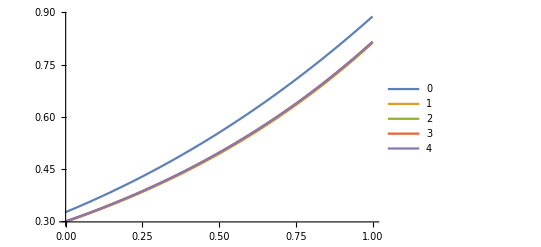

```mathematica
Plot[Evaluate[Table[Josh[k]/. {x->0.5, t->1,γ->1},{k,0, 5}]],{y,0,1},PlotLegends->{Table[k,{k,0,4}]}]
```

```mathematica
Plot[{SimplifiedHayward[3] /. {x->0.5,t -> 0.001, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111}, GaussianApprox/. {x->0.5,t -> 0.001, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111}}, {y,0,1}, PlotLabels->{"Pertur", "Gaussian"}]
```

-Graphics-

```mathematica
tmp[y_,t_] = Evaluate[GaussianApprox /. {x->0.5, Ne->500,α->0.005, Λ -> 1, W->1}];
joshtmp[y_,t_] = Evaluate[Josh[3]/.{x->0.5,γ->5}];
haywardtmp[y_,t_,VG_] = Evaluate[SimplifiedHayward[3]/. {x->0.5,Ne->500,α->0.005, Λ -> 1, W->1}];
```

```mathematica
Clear[Anim];
Anim=Table[Plot[{haywardtmp[y,t,0.00001111],joshtmp[y,t],tmp[y,t]},
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLegends->TextString@Row@{"T=",t}, 
PlotLabels->{"Hayward","Josh", "Gaussian"},
PlotRange->{{0,1},{-5,5}}],
{t,.001,.5,.025}]
```

```mathematica
Export["TimeComparison.gif",Anim,"DisplayDurations"->0.75]
```

```mathematica
Plot[{haywardtmp[y,0.25,0.00001111],joshtmp[y,0.25],tmp[y,0.25]},
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLabels->{"Hayward","Josh", "Gaussian"},
PlotLegends->TextString@Row@{"T=",0.25}, 
PlotRange->{{0,1},{-1,4}}]
```

-Graphics-

```mathematica
Clear[Anim];
Anim=Table[Plot[{haywardtmp[y,0.1,VG],joshtmp[y,0.1],tmp[y,0.1]},
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLegends->TextString@Row@{"VG=",NumberForm[VG, {6,5}]}, 
PlotLabels->{"Hayward","Josh", "Gaussian"},
PlotRange->{{0,1},{0,10}}],
{VG,.000011111,.11111, 0.005}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export["VGComparison.gif",Anim,"DisplayDurations"->0.75]
```

VGComparison.gif

```mathematica
Export["C:\\Users\\natha\\Documents\\25gencomparison.svg",%59,"SVG"]
```

C:\Users\natha\Documents\25gencomparison.svg

```mathematica
Export["C:\\Users\\natha\\Documents\\10gencomparison.svg",%54,"SVG"]
```

C:\Users\natha\Documents\10gencomparison.svg

```mathematica
Export["C:\\Users\\natha\\Documents\\5gencomparison.svg",%51,"SVG"]
```

C:\Users\natha\Documents\5gencomparison.svg

```mathematica
Export["C:\\Users\\natha\\Documents\\1gencomparison.svg",%43,"SVG"]
```

C:\Users\natha\Documents\1gencomparison.svg

```mathematica
Manipulate[Plot[tmp[y,t], {y,0,1}], {t,0.01,1}]
```

```mathematica
Manipulate[Plot[joshtmp[y,t],{y,0,1}],{t,0.01,1}]
```

```mathematica
Manipulate[Plot[haywardtmp[y,t,VG],{y,0,1}],{t,0.01,1},{VG,.0000011111,.11111}, ContinuousAction->False]
```

```mathematica
Manipulate[Plot[{joshtmp[y,t],tmp[y,t]},{y,0,1},PlotLabels->{"Josh", "Gaussian"}],{t,0.01,1}]
```

```mathematica
Manipulate[Plot[{haywardtmp[y,t,VG],joshtmp[y,t],tmp[y,t]},{y,0,1},PlotLabels->{"Hayward","Josh", "Gaussian"}],{t,0.01,1},{VG,.0000011111000001,.11111000001}, ContinuousAction->False]
```

```mathematica
Integrate[neutral,y]/. {x->0.5, t->.1}
```

0.00613016 (0.+6.37437 y-187.488 y^2+2716.73 y^3-16725.4 y^4+73563.3 y^5-163001. y^6+183897. y^7-102994. y^8+22887.6 y^9)

```mathematica
Integrate[neutral/. {x->0.5, t->.1},y] == 0.95
```

0.0390759 y-1.14933 y^2+16.654 y^3-102.529 y^4+450.955 y^5-999.222 y^6+1127.32 y^7-631.37 y^8+140.304 y^9==0.95

```mathematica
Solve[0.03907591274514233 y-1.1493331469045316 y^2+16.653962992566708 y^3-102.52910529373233 y^4+450.95465181487157 y^5-999.221727216257 y^6+1127.3186613744713 y^7-631.3700544845127 y^8+140.30445655211392 y^9==0.95,{y},Reals]
```

{{y→0.754255}}

```mathematica
Integrate[neutral,y] == 0.95
```

```mathematica
neutInt = Integrate[neutral,y]
```

6 ⅇ^(-55 t) (1-x) x (ⅇ^(54 t) y-5 ⅇ^(52 t) (-1+2 x) y+14 ⅇ^(49 t) (1-5 x+5 x^2) y-30 ⅇ^(45 t) (-1+9 x-21 x^2+14 x^3) y+55 ⅇ^(40 t) (1-14 x+56 x^2-84 x^3+42 x^4) y-91 ⅇ^(34 t) (-1+20 x-120 x^2+300 x^3-330 x^4+132 x^5) y+140 ⅇ^(27 t) (1-27 x+225 x^2-825 x^3+1485 x^4-1287 x^5+429 x^6) y-204 ⅇ^(19 t) (-1+35 x-385 x^2+1925 x^3-5005 x^4+7007 x^5-5005 x^6+1430 x^7) y+285 ⅇ^(10 t) (1-44 x+616 x^2-4004 x^3+14014 x^4-28028 x^5+32032 x^6-19448 x^7+4862 x^8) y-385 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y+5 ⅇ^(52 t) (-1+2 x) y^2-35 ⅇ^(49 t) (1-5 x+5 x^2) y^2+135 ⅇ^(45 t) (-1+9 x-21 x^2+14 x^3) y^2-385 ⅇ^(40 t) (1-14 x+56 x^2-84 x^3+42 x^4) y^2+910 ⅇ^(34 t) (-1+20 x-120 x^2+300 x^3-330 x^4+132 x^5) y^2-1890 ⅇ^(27 t) (1-27 x+225 x^2-825 x^3+1485 x^4-1287 x^5+429 x^6) y^2+3570 ⅇ^(19 t) (-1+35 x-385 x^2+1925 x^3-5005 x^4+7007 x^5-5005 x^6+1430 x^7) y^2-6270 ⅇ^(10 t) (1-44 x+616 x^2-4004 x^3+14014 x^4-28028 x^5+32032 x^6-19448 x^7+4862 x^8) y^2+10395 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y^2+70/3 ⅇ^(49 t) (1-5 x+5 x^2) y^3-210 ⅇ^(45 t) (-1+9 x-21 x^2+14 x^3) y^3+3080/3 ⅇ^(40 t) (1-14 x+56 x^2-84 x^3+42 x^4) y^3-3640 ⅇ^(34 t) (-1+20 x-120 x^2+300 x^3-330 x^4+132 x^5) y^3+10500 ⅇ^(27 t) (1-27 x+225 x^2-825 x^3+1485 x^4-1287 x^5+429 x^6) y^3-26180 ⅇ^(19 t) (-1+35 x-385 x^2+1925 x^3-5005 x^4+7007 x^5-5005 x^6+1430 x^7) y^3+58520 ⅇ^(10 t) (1-44 x+616 x^2-4004 x^3+14014 x^4-28028 x^5+32032 x^6-19448 x^7+4862 x^8) y^3-120120 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y^3+105 ⅇ^(45 t) (-1+9 x-21 x^2+14 x^3) y^4-1155 ⅇ^(40 t) (1-14 x+56 x^2-84 x^3+42 x^4) y^4+6825 ⅇ^(34 t) (-1+20 x-120 x^2+300 x^3-330 x^4+132 x^5) y^4-28875 ⅇ^(27 t) (1-27 x+225 x^2-825 x^3+1485 x^4-1287 x^5+429 x^6) y^4+98175 ⅇ^(19 t) (-1+35 x-385 x^2+1925 x^3-5005 x^4+7007 x^5-5005 x^6+1430 x^7) y^4-285285 ⅇ^(10 t) (1-44 x+616 x^2-4004 x^3+14014 x^4-28028 x^5+32032 x^6-19448 x^7+4862 x^8) y^4+735735 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y^4+462 ⅇ^(40 t) (1-14 x+56 x^2-84 x^3+42 x^4) y^5-6006 ⅇ^(34 t) (-1+20 x-120 x^2+300 x^3-330 x^4+132 x^5) y^5+41580 ⅇ^(27 t) (1-27 x+225 x^2-825 x^3+1485 x^4-1287 x^5+429 x^6) y^5-204204 ⅇ^(19 t) (-1+35 x-385 x^2+1925 x^3-5005 x^4+7007 x^5-5005 x^6+1430 x^7) y^5+798798 ⅇ^(10 t) (1-44 x+616 x^2-4004 x^3+14014 x^4-28028 x^5+32032 x^6-19448 x^7+4862 x^8) y^5-2648646 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y^5+2002 ⅇ^(34 t) (-1+20 x-120 x^2+300 x^3-330 x^4+132 x^5) y^6-30030 ⅇ^(27 t) (1-27 x+225 x^2-825 x^3+1485 x^4-1287 x^5+429 x^6) y^6+238238 ⅇ^(19 t) (-1+35 x-385 x^2+1925 x^3-5005 x^4+7007 x^5-5005 x^6+1430 x^7) y^6-1331330 ⅇ^(10 t) (1-44 x+616 x^2-4004 x^3+14014 x^4-28028 x^5+32032 x^6-19448 x^7+4862 x^8) y^6+5885880 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y^6+8580 ⅇ^(27 t) (1-27 x+225 x^2-825 x^3+1485 x^4-1287 x^5+429 x^6) y^7-145860 ⅇ^(19 t) (-1+35 x-385 x^2+1925 x^3-5005 x^4+7007 x^5-5005 x^6+1430 x^7) y^7+1304160 ⅇ^(10 t) (1-44 x+616 x^2-4004 x^3+14014 x^4-28028 x^5+32032 x^6-19448 x^7+4862 x^8) y^7-8168160 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y^7+36465 ⅇ^(19 t) (-1+35 x-385 x^2+1925 x^3-5005 x^4+7007 x^5-5005 x^6+1430 x^7) y^8-692835 ⅇ^(10 t) (1-44 x+616 x^2-4004 x^3+14014 x^4-28028 x^5+32032 x^6-19448 x^7+4862 x^8) y^8+6891885 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y^8+461890/3 ⅇ^(10 t) (1-44 x+616 x^2-4004 x^3+14014 x^4-28028 x^5+32032 x^6-19448 x^7+4862 x^8) y^9-3233230 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y^9+646646 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y^10)

```mathematica
temporary = neutInt /. {y->0};
AUC = neutInt - temporary
clear[temporary];
```

6 ⅇ^(-55 t) (1-x) x (ⅇ^(54 t) y-5 ⅇ^(52 t) (-1+2 x) y+14 ⅇ^(49 t) (1-5 x+5 x^2) y-30 ⅇ^(45 t) (-1+9 x-21 x^2+14 x^3) y+55 ⅇ^(40 t) (1-14 x+56 x^2-84 x^3+42 x^4) y-91 ⅇ^(34 t) (-1+20 x-120 x^2+300 x^3-330 x^4+132 x^5) y+140 ⅇ^(27 t) (1-27 x+225 x^2-825 x^3+1485 x^4-1287 x^5+429 x^6) y-204 ⅇ^(19 t) (-1+35 x-385 x^2+1925 x^3-5005 x^4+7007 x^5-5005 x^6+1430 x^7) y+285 ⅇ^(10 t) (1-44 x+616 x^2-4004 x^3+14014 x^4-28028 x^5+32032 x^6-19448 x^7+4862 x^8) y-385 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y+5 ⅇ^(52 t) (-1+2 x) y^2-35 ⅇ^(49 t) (1-5 x+5 x^2) y^2+135 ⅇ^(45 t) (-1+9 x-21 x^2+14 x^3) y^2-385 ⅇ^(40 t) (1-14 x+56 x^2-84 x^3+42 x^4) y^2+910 ⅇ^(34 t) (-1+20 x-120 x^2+300 x^3-330 x^4+132 x^5) y^2-1890 ⅇ^(27 t) (1-27 x+225 x^2-825 x^3+1485 x^4-1287 x^5+429 x^6) y^2+3570 ⅇ^(19 t) (-1+35 x-385 x^2+1925 x^3-5005 x^4+7007 x^5-5005 x^6+1430 x^7) y^2-6270 ⅇ^(10 t) (1-44 x+616 x^2-4004 x^3+14014 x^4-28028 x^5+32032 x^6-19448 x^7+4862 x^8) y^2+10395 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y^2+70/3 ⅇ^(49 t) (1-5 x+5 x^2) y^3-210 ⅇ^(45 t) (-1+9 x-21 x^2+14 x^3) y^3+3080/3 ⅇ^(40 t) (1-14 x+56 x^2-84 x^3+42 x^4) y^3-3640 ⅇ^(34 t) (-1+20 x-120 x^2+300 x^3-330 x^4+132 x^5) y^3+10500 ⅇ^(27 t) (1-27 x+225 x^2-825 x^3+1485 x^4-1287 x^5+429 x^6) y^3-26180 ⅇ^(19 t) (-1+35 x-385 x^2+1925 x^3-5005 x^4+7007 x^5-5005 x^6+1430 x^7) y^3+58520 ⅇ^(10 t) (1-44 x+616 x^2-4004 x^3+14014 x^4-28028 x^5+32032 x^6-19448 x^7+4862 x^8) y^3-120120 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y^3+105 ⅇ^(45 t) (-1+9 x-21 x^2+14 x^3) y^4-1155 ⅇ^(40 t) (1-14 x+56 x^2-84 x^3+42 x^4) y^4+6825 ⅇ^(34 t) (-1+20 x-120 x^2+300 x^3-330 x^4+132 x^5) y^4-28875 ⅇ^(27 t) (1-27 x+225 x^2-825 x^3+1485 x^4-1287 x^5+429 x^6) y^4+98175 ⅇ^(19 t) (-1+35 x-385 x^2+1925 x^3-5005 x^4+7007 x^5-5005 x^6+1430 x^7) y^4-285285 ⅇ^(10 t) (1-44 x+616 x^2-4004 x^3+14014 x^4-28028 x^5+32032 x^6-19448 x^7+4862 x^8) y^4+735735 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y^4+462 ⅇ^(40 t) (1-14 x+56 x^2-84 x^3+42 x^4) y^5-6006 ⅇ^(34 t) (-1+20 x-120 x^2+300 x^3-330 x^4+132 x^5) y^5+41580 ⅇ^(27 t) (1-27 x+225 x^2-825 x^3+1485 x^4-1287 x^5+429 x^6) y^5-204204 ⅇ^(19 t) (-1+35 x-385 x^2+1925 x^3-5005 x^4+7007 x^5-5005 x^6+1430 x^7) y^5+798798 ⅇ^(10 t) (1-44 x+616 x^2-4004 x^3+14014 x^4-28028 x^5+32032 x^6-19448 x^7+4862 x^8) y^5-2648646 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y^5+2002 ⅇ^(34 t) (-1+20 x-120 x^2+300 x^3-330 x^4+132 x^5) y^6-30030 ⅇ^(27 t) (1-27 x+225 x^2-825 x^3+1485 x^4-1287 x^5+429 x^6) y^6+238238 ⅇ^(19 t) (-1+35 x-385 x^2+1925 x^3-5005 x^4+7007 x^5-5005 x^6+1430 x^7) y^6-1331330 ⅇ^(10 t) (1-44 x+616 x^2-4004 x^3+14014 x^4-28028 x^5+32032 x^6-19448 x^7+4862 x^8) y^6+5885880 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y^6+8580 ⅇ^(27 t) (1-27 x+225 x^2-825 x^3+1485 x^4-1287 x^5+429 x^6) y^7-145860 ⅇ^(19 t) (-1+35 x-385 x^2+1925 x^3-5005 x^4+7007 x^5-5005 x^6+1430 x^7) y^7+1304160 ⅇ^(10 t) (1-44 x+616 x^2-4004 x^3+14014 x^4-28028 x^5+32032 x^6-19448 x^7+4862 x^8) y^7-8168160 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y^7+36465 ⅇ^(19 t) (-1+35 x-385 x^2+1925 x^3-5005 x^4+7007 x^5-5005 x^6+1430 x^7) y^8-692835 ⅇ^(10 t) (1-44 x+616 x^2-4004 x^3+14014 x^4-28028 x^5+32032 x^6-19448 x^7+4862 x^8) y^8+6891885 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y^8+461890/3 ⅇ^(10 t) (1-44 x+616 x^2-4004 x^3+14014 x^4-28028 x^5+32032 x^6-19448 x^7+4862 x^8) y^9-3233230 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y^9+646646 (-1+54 x-936 x^2+7644 x^3-34398 x^4+91728 x^5-148512 x^6+143208 x^7-75582 x^8+16796 x^9) y^10)

```mathematica
Solve[(AUC /. {x->0.2, t ->0.1}) == 0.95,{y},Reals]
```

{{y→0.44926},{y→1.44873}}